```mathematica
Clear["Global`*"]
```

```mathematica
Omegak=(G Msun/r^3)^(1/2);
```

```mathematica
Td = T0 (r/r0)^(-bT);
cd = Sqrt[kb Td / (mu mp)];
Hd = cd / Omegak;
Sigmad = Sigma0 (r/r0)^(-bS);
rhod = 1/Sqrt[2 Pi] Sigmad / Hd;
lambda=1/(Sqrt[2 Pi] sigma (rhod / (mu mp)));
bS=1/2+bT+d;
vk=Omegak r;
eta=cd^2/(2 vk^2);
(*taus=4 rhos s^2/(9 rhod cd lambda) Omegak;*)
taus=rhos s /(rhod cd) Omegak;
```

```mathematica
tr = taus / (2 eta Omegak) (*taus>>1*)
```

(G mp Msun mu √(2 π) (r/r0)^(1/2+2 bT+d) rhos s)/(kb √((G Msun)/r^3) r Sigma0 T0)

```mathematica
(*tr=1/(2 eta Omegak taus)*) (*taus<<1*)
```

(G mp Msun mu (r/r0)^(-1/2-d) Sigma0)/(kb √(2 π) √((G Msun)/r^3) r rhos s T0)

```mathematica
Simplify[tr]
```

(mp mu √((G Msun)/r^3) r (r/r0)^(1/2-d) r0 Sigma0)/(kb √(2 π) rhos s T0)

```mathematica
tr[r_]:=A r^(-d);
```

```mathematica
tdes[r_]:=B Exp[c r^(bT)];
```

```mathematica
sol = Solve[tr[r] == tdes[r], r]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{r→((d ProductLog[((B/A)^(-bT/d) bT c)/d])/(bT c))^(1/bT)}}

```mathematica
r1[s]
```

r1[s]

```mathematica
r1=r/.sol[[1]]
```

2^(-1/bT) (((-4+bT) ProductLog[(((2^(-1/2+2/bT) B)/A)^(-(2 bT)/(-4+bT)) bT c)/(-4+bT)])/(bT c))^(1/bT)

```mathematica
FullSimplify[r1]
```

2^(-1/bT) (((-4+bT) ProductLog[(((2^(-1/2+2/bT) B)/A)^(-(2 bT)/(-4+bT)) bT c)/(-4+bT)])/(bT c))^(1/bT)

```mathematica
G = 6.67 10^(-8);
Msun=2 10^33;
T0=120;
bT=3/7;
kb=1.38 10^(-16);
mu=2.3;
mp=1.67 10^(-24);
Sigma0=2000;
d=1/14;
rhos=2;
mux=18;
Nx=10^15;
Ex=5800;
nux=1.6 10^11Sqrt[Ex/mux];
AU=1.5 10^13;
r0=AU;
```

```mathematica
A[s_]:=Sqrt[G Msun] mu mp Sigma0 r0^(1/2-d)/(Sqrt[2 Pi] kb rhos s T0);
```

```mathematica
B[s_]:=rhos s/(3 mux mp Nx nux);
c=Ex r0^-bT/T0;
```

```mathematica
r1[s_]:=(d ProductLog[(B[s]/A[s])^(-bT/d) bT c/d]/(bT c))^(1/bT)
```

```mathematica
s=0.01;
```

```mathematica
r1[1]/AU
```

0.520505

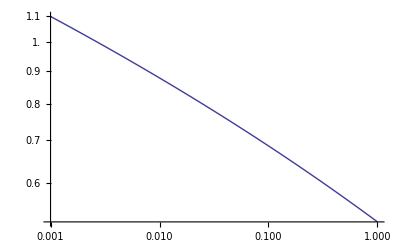

```mathematica
LogLogPlot[r1[s]/AU, {s, 0.001, 1}]
```

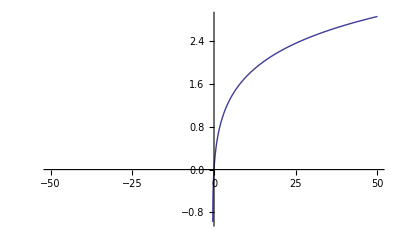

```mathematica
Plot[ProductLog[x], {x, -50, 50}]
```

```mathematica
ProductLog[-2.5]
```

0.334081+1.75854 ⅈ

```mathematica
ProductLog[2.5]
```

0.958586

```mathematica
(tr[r]-tdes[r]==0)/.{{r->r1}}
```

{-B ⅇ^(c ((-(d ProductLog[-((B/A)^(bT/d) bT c)/d])/(bT c))^(1/bT))^bT)+A ((-(d ProductLog[-((B/A)^(bT/d) bT c)/d])/(bT c))^(1/bT))^d==0}